```mathematica
LogisticEquation = y'[t]==r(1-(y[t]/K))*y[t];
DSolve[{LogisticEquation/.{r-> -1,K->7},y[0]==5}, y,t]
```

Solve::ifun: 逆関数がSolveで使われているため，求められない解がある可能性があります．解の詳細情報にはReduceをお使いください．

{{y→Function[{t},35/(5+2 ⅇ^t)]}}

```mathematica
Function[{t},-210/(-30+23 ⅇ^t)]
```

Function[{t},-210/(-30+23 ⅇ^t)]

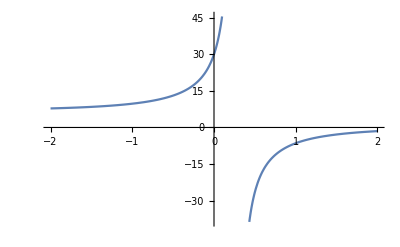

```mathematica
Plot[Function[{t},-210/(-30+23 ⅇ^t)][x],{x,-2.,2.}]
```

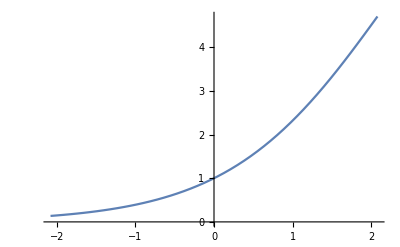

```mathematica
Plot[(10 ⅇ^t)/(9+ⅇ^t),{t,-2.0794415416798357,2.0794415416798357}]
```

```mathematica
Function[{t},35/(5+2 ⅇ^t)]
```

Function[{t},35/(5+2 ⅇ^t)]

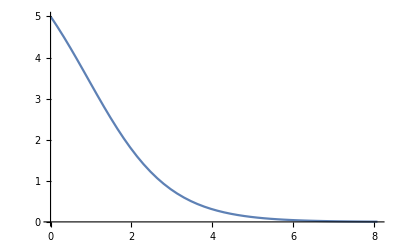

```mathematica
Plot[Function[{t},35/(5+2 ⅇ^t)][x],{x,0,8.07944}]
```